## Importação dos arquivos com os resultados das análises

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
semz1=ToExpression[Import["FM_I_0.0.list","List"]];
semz2=ToExpression[Import["FM_II_0.0.list","List"]];
semz3=ToExpression[Import["FM_III_0.0.list","List"]];
```

```mathematica
(*Erro de 0.02*)
comzI02=ToExpression[Import["FM_I_0.02.list","List"]];
comzII02=ToExpression[Import["FM_II_0.02.list","List"]];
comzIII02=ToExpression[Import["FM_III_0.02.list","List"]];
```

```mathematica
(*Erro de 0.01*)
comzI01=ToExpression[Import["FM_I_0.01.list","List"]];
comzII01=ToExpression[Import["FM_II_0.01.list","List"]];
comzIII01=ToExpression[Import["FM_III_0.01.list","List"]];
```

```mathematica
(*Erro de 0.002*)
comzI002=ToExpression[Import["FM_I_0.002.list","List"]];
comzII002=ToExpression[Import["FM_II_0.002.list","List"]];
comzIII002=ToExpression[Import["FM_III_0.002.list","List"]];
```

## Plots com as comparações

### Comparação entre o caso sem erro e erro de 0.02

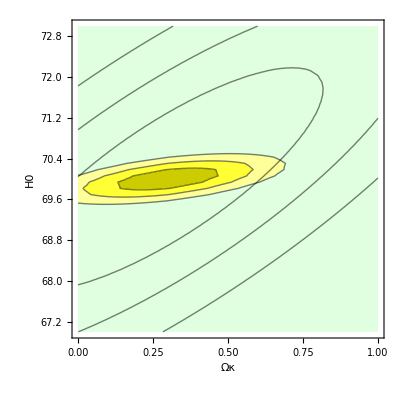

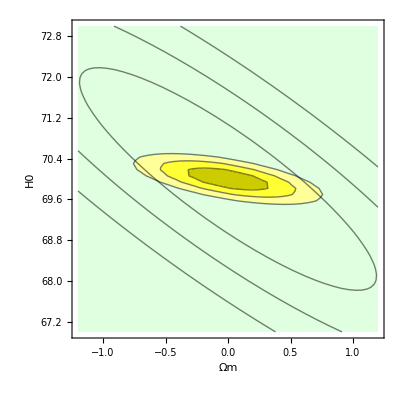

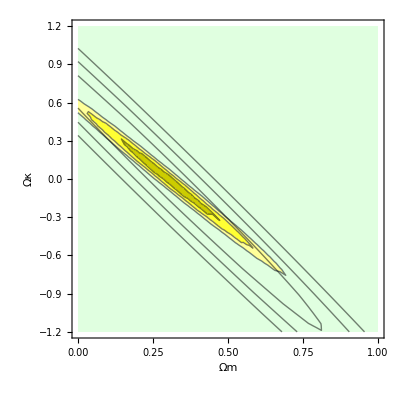

```mathematica
(*Comparação entre o caso sem erro e erro de 0.02*)
compare1=ListContourPlot[{semz1,comzI02},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωκ","H0"}]

compare2=ListContourPlot[{semz2,comzII02},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","H0"}]

compare3=ListContourPlot[{semz3,comzIII02},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
```

### Comparação entre o caso sem erro e erro de 0.002

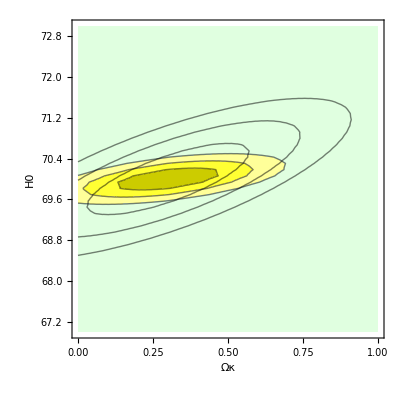

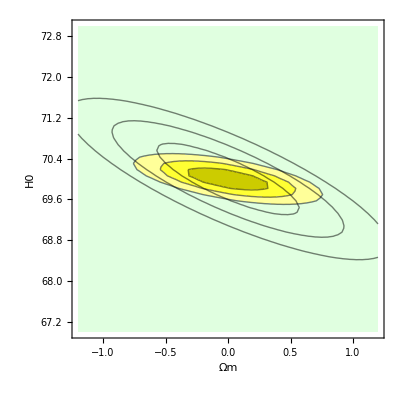

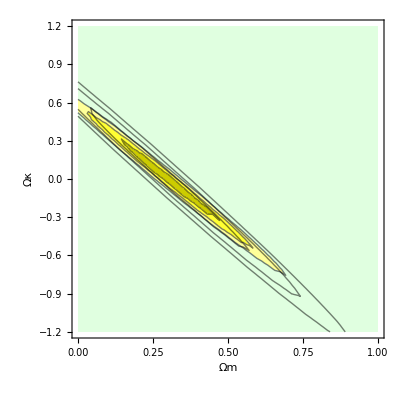

```mathematica
(*Comparação entre o caso sem erro e erro de 0.002*)
compare1=ListContourPlot[{semz1,comzI002},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωκ","H0"}]

compare2=ListContourPlot[{semz2,comzII002},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","H0"}]

compare3=ListContourPlot[{semz3,comzIII002},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
```

### Comparação entre o caso sem erro e erro de 0.01

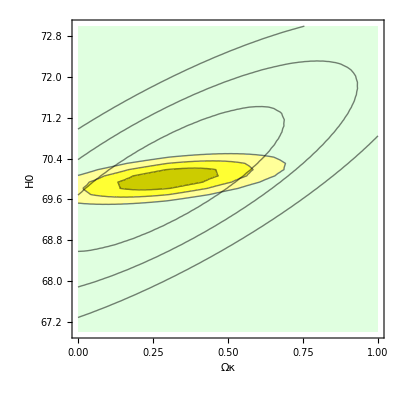

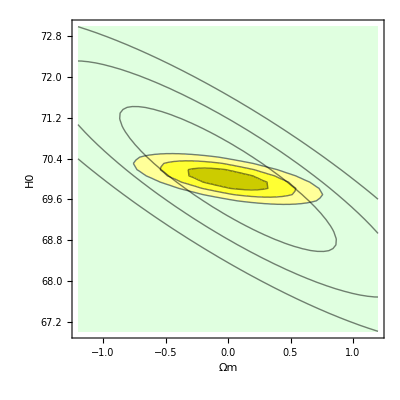

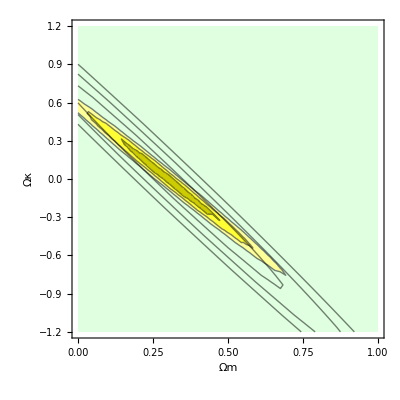

```mathematica
(*Comparação entre o caso sem erro e erro de 0.01*)
compare1=ListContourPlot[{semz1,comzI01},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωκ","H0"}]

compare2=ListContourPlot[{semz2,comzII01},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","H0"}]

compare3=ListContourPlot[{semz3,comzIII01},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
```

### Comparação entre os casos sem erro, erro de 0.02 e erro de 0.002

```mathematica
(*Comparação entre os casos sem erro, erro de 0.02 e erro de 0.002*)
```

```mathematica
plotfun[lhood_,cstyle_,cshade_,label_]:=Module[{},ListContourPlot[lhood,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->cshade,Frame->True,FrameLabel->label,ContourStyle->cstyle]];
cshadesem={Darker[Yellow,.2],Lighter[Yellow,.2],Lighter[Yellow,.6],White};
```

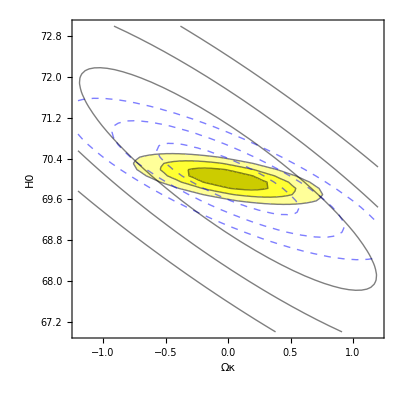

```mathematica
psem1=plotfun[semz1,Automatic,cshadesem,{"Ωκ","H0"}];
pcomzI002=plotfun[comzI002,Directive[Thick,Dashed,Blue],Transparent,{"Ωκ","H0"}];
pcomzI02=plotfun[comzI02,Black,Transparent,{"Ωκ","H0"}];

Show[psem1,pcomzI002,pcomzI02]
```

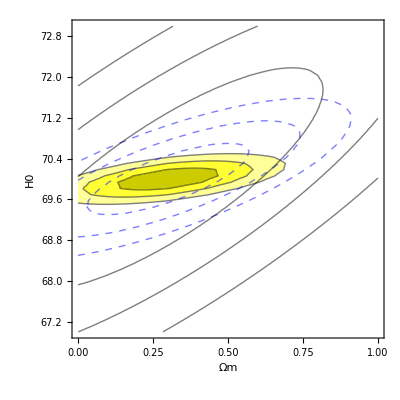

```mathematica
psem2=plotfun[semz2,Automatic,cshadesem,{"Ωm","H0"}];
pcomzII002=plotfun[comzII002,Directive[Thick,Dashed,Blue],Transparent,{"Ωm","H0"}];
pcomzII02=plotfun[comzII02,Black,Transparent,{"Ωm","H0"}];

Show[psem2,pcomzII002,pcomzII02]
```

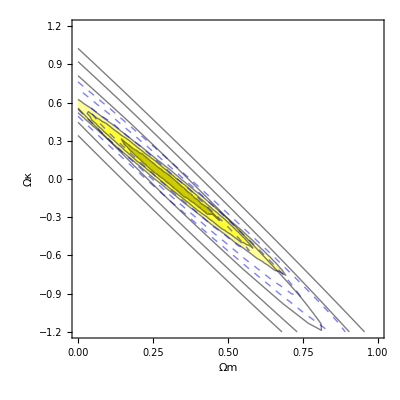

```mathematica
psem3=plotfun[semz3,Automatic,cshadesem,{"Ωm","Ωκ"}];
pcomzIII002=plotfun[comzIII002,Directive[Thick,Dashed,Blue],Transparent,{"Ωm","Ωκ"}];
pcomzIII02=plotfun[comzIII02,Black,Transparent,{"Ωm","Ωκ"}];

Show[psem3,pcomzIII002,pcomzIII02]
```